### Adaptively evolving a sorting algorithm

#### Init

```mathematica
Module[
{deep=4000},
SeedRandom[426779];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
caf = CellularAutomaton[ru, {Join[Table[1,5], Table[2, 5]] ,0},{{{10}}, 9}],
loss = Count[Join[Table[2, 5], Table[1,5]] - caf, Except[0]],
If[loss<=Last[#],{ru,loss},#]
]&,{{0,3,1},Infinity},deep]];
```

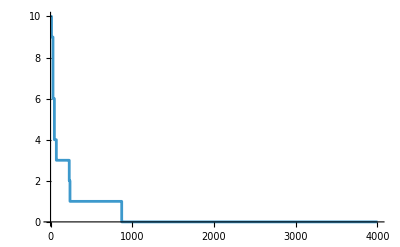

```mathematica
ListStepPlot[evo[[All, -1]], PlotRange->All]
```

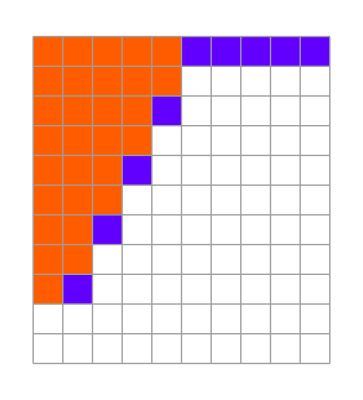
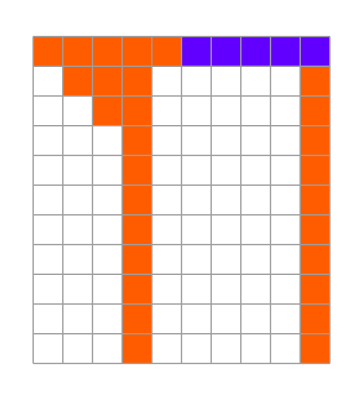
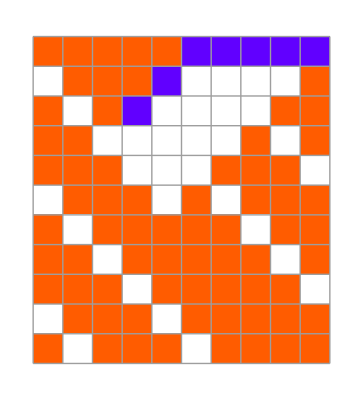
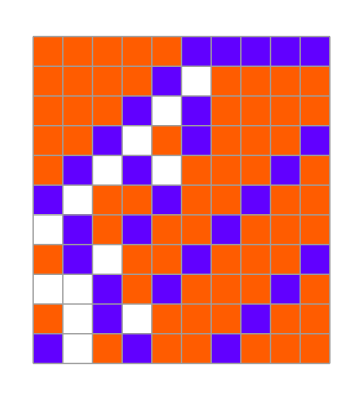
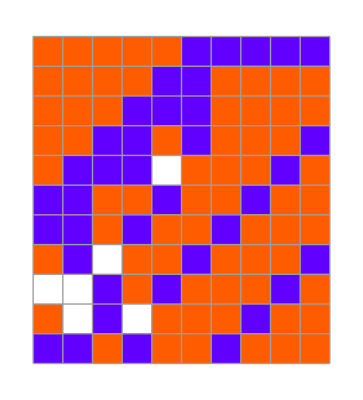
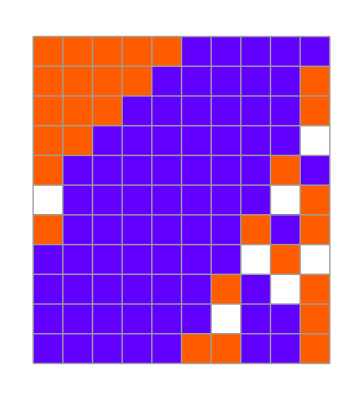
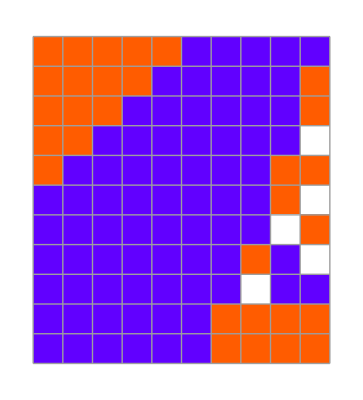
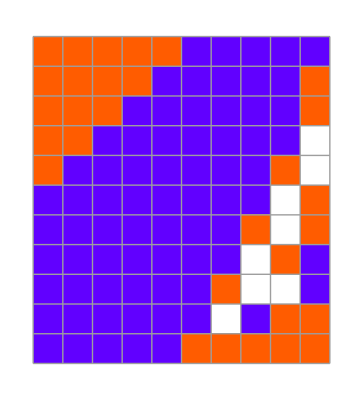

```mathematica
ArrayPlot[CellularAutomaton[#,{Join[Table[1,5], Table[2, 5]], 0}, {10, 9}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True]&/@ GatherBy[evo, Last][[2;;, -1, 1]]
```

```mathematica
Module[
{deep=4000},
SeedRandom[426780];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
caf = CellularAutomaton[ru, {Join[Table[1,5], Table[2, 5]] ,0},{{{10}}, 9}],
loss = Count[Join[Table[2, 5], Table[1,5]] - caf, Except[0]],
If[loss<=Last[#],{ru,loss},#]
]&,{{0,3,1},Infinity},deep]];
```

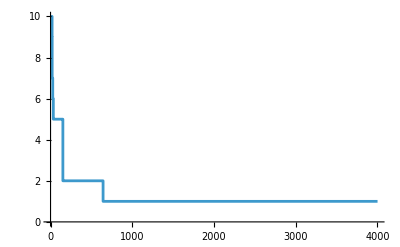

```mathematica
ListStepPlot[evo[[All, -1]], PlotRange->All]
```

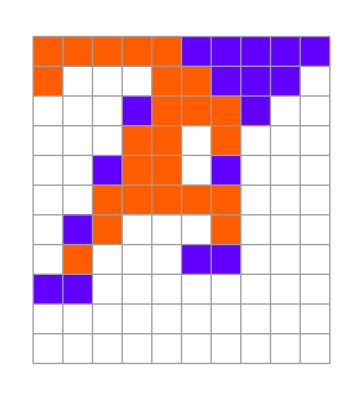
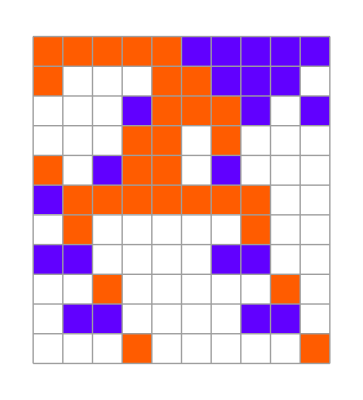
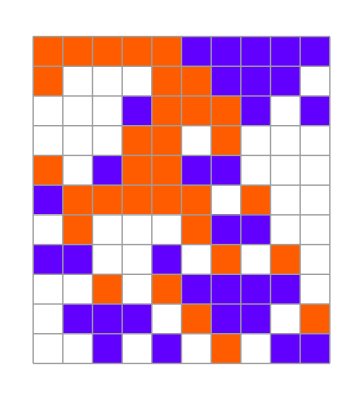
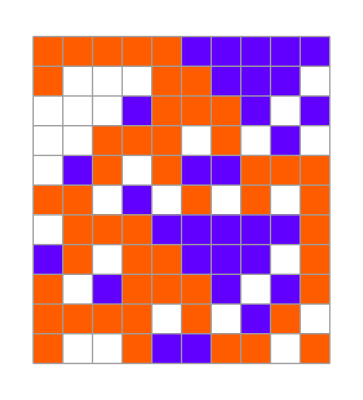
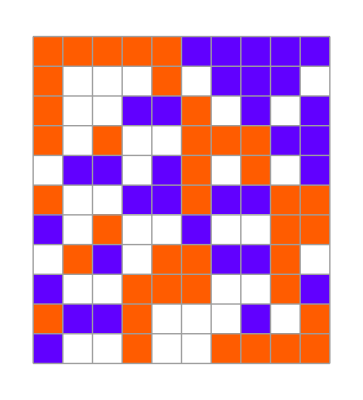
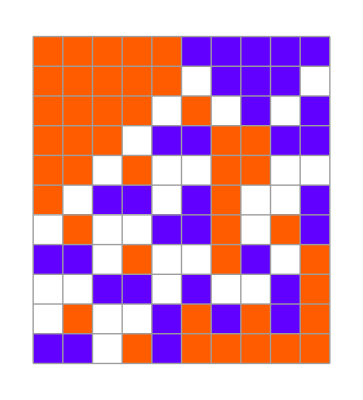
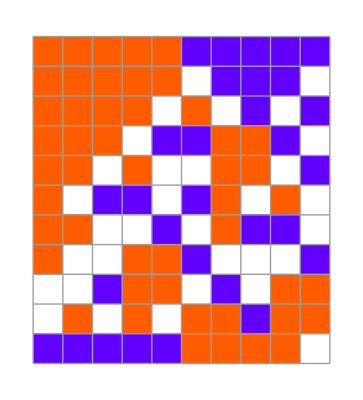

```mathematica
ArrayPlot[CellularAutomaton[#,{Join[Table[1,5], Table[2, 5]], 0}, {10, 9}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True]&/@ GatherBy[evo, Last][[2;;, -1, 1]]
```

```mathematica
Module[
{deep=4000},
SeedRandom[426781];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
caf = CellularAutomaton[ru, {Join[Table[1,5], Table[2, 5]] ,0},{{{10}}, 9}],
loss = Count[Join[Table[2, 5], Table[1,5]] - caf, Except[0]],
If[loss<=Last[#],{ru,loss},#]
]&,{{0,3,1},Infinity},deep]];
```

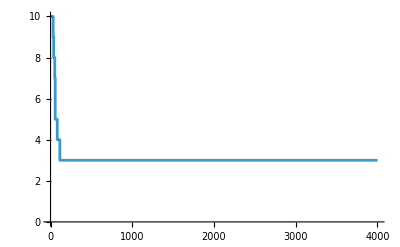

```mathematica
ListStepPlot[evo[[All, -1]], PlotRange->All]
```

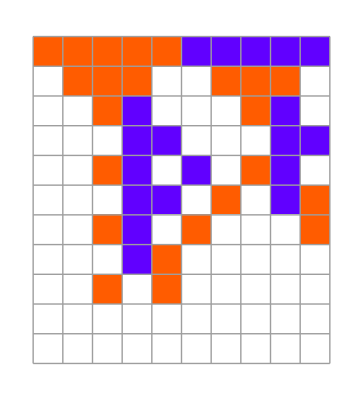
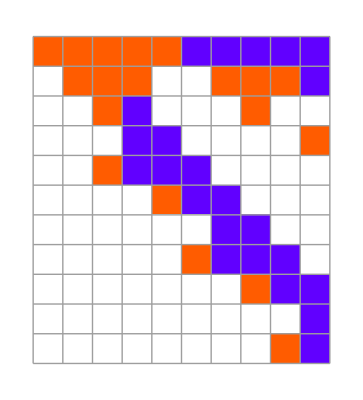
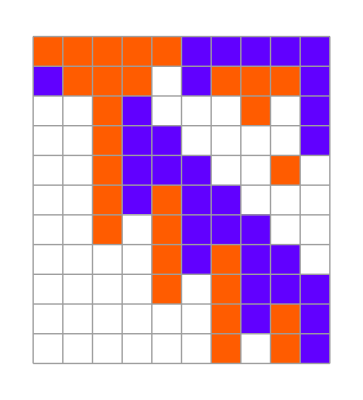
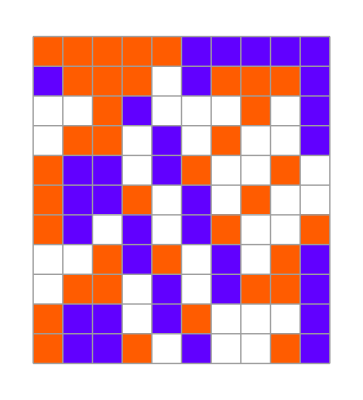
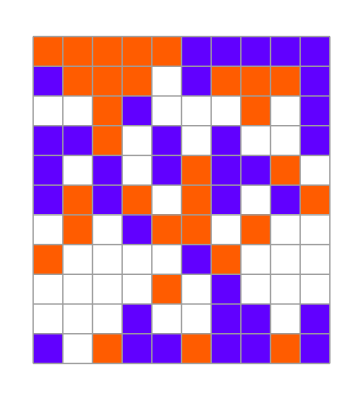
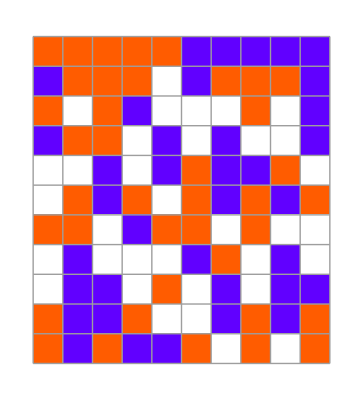
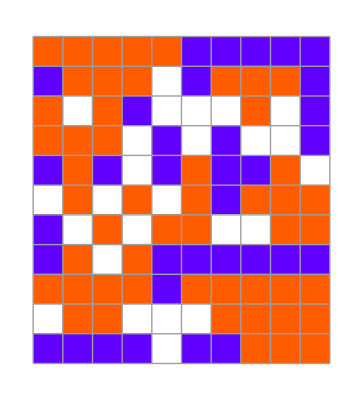

```mathematica
ArrayPlot[CellularAutomaton[#,{Join[Table[1,5], Table[2, 5]], 0}, {10, 9}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True]&/@ GatherBy[evo, Last][[2;;, -1, 1]]
```

#### Conserving “molecules”

```mathematica
MapAt[f, 1->2, 1]
```

f[1]→2

```mathematica
Delete[{0, 1, 2}, 2]
```

{0,2}

```mathematica
ClearAll[RandomBlockRuleMutation]
RandomBlockRuleMutation[rus_, k_]:= 
Module[{(*bitidx, newbit, outbitidx*)},
ruidx = RandomInteger[{1, Length[rus]}];
bitidx = RandomInteger[{1, Length[rus[[ruidx, 1]]]}];
newbit = RandomChoice[Delete[Range[0, k - 1], rus[[ruidx,1, bitidx]] + 1]];
outbitidx = RandomChoice[Select[Range[Length[rus[[ruidx, 2]]]], rus[[ruidx, 2, #]]!=newbit&]];
ReplacePart[rus, {{ruidx,1, bitidx}->newbit, {ruidx,2, outbitidx}->newbit }]]
```

```mathematica
RandomBlockRuleMutation[{{1,0}->{0,1},{0,1}->{1,0},{1,2}->{0,2},
{2,1}->{2,0},{2,0}->{1,2},{0,2}->{2,1},
{1,1}->{2,2},{0,0}->{0,0},{2,2}->{1,1}}, 3]
```

{{2,0}→{0,2},{0,1}→{1,0},{1,2}→{0,2},{2,1}→{2,0},{2,0}→{1,2},{0,2}→{2,1},{1,1}→{2,2},{0,0}→{0,0},{2,2}→{1,1}}

```mathematica
Table[Map[ArrayPlot[{#},ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True, ImageSize->20]&, DeleteCases[#, x_->x_], {2}]&[
RandomBlockRuleMutation[{{1,0}->{0,1},{0,1}->{1,0},{1,2}->{0,2},
{2,1}->{2,0},{2,0}->{1,2},{0,2}->{2,1},
{1,1}->{2,2},{0,0}->{0,0},{2,2}->{1,1}}, 3]], 5]
```

{{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-},{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-},{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-},{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-},{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}}

```mathematica
ruidx
```

3

```mathematica
bitidx
```

1

```mathematica
newbit
```

2

```mathematica
outbitidx
```

RandomChoice[{}]

```mathematica
rus = {{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},{0,1}->{0,1},{0,0}->{0,0}};
```

```mathematica
RandomChoice[Select[Range[Length[rus[[ruidx, 2]]]], rus[[ruidx, 2, #]]!=newbit&]]
```

1

```mathematica
ReplacePart[{{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},{0,1}->{0,1},{0,0}->{0,0}}, {{ruidx,1, bitidx}->newbit, {ruidx,2, outbitidx}->newbit }]
```

{{2,2}→{1,1},{1,1}→{2,2},{2,2}→{2,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}}

```mathematica
SeedRandom[1];RandomBlockRuleMutation[{{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},{0,1}->{0,1},{0,0}->{0,0}}, 3]
```

RandomChoice::lrwl: The items for choice {} should be a non-empty list or a rule weights -> choices.

ReplacePart::pkspec1: The expression RandomChoice[{}] cannot be used as a part specification.

{{2,2}→{1,1},{2,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}}

```mathematica
Table[Echo[i];SeedRandom[i];RandomBlockRuleMutation[{{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},{0,1}->{0,1},{0,0}->{0,0}}, 3], {i, 30}]
```

1

RandomChoice::lrwl: The items for choice {} should be a non-empty list or a rule weights -> choices.

ReplacePart::pkspec1: The expression RandomChoice[{}] cannot be used as a part specification.

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

RandomChoice::lrwl: The items for choice {} should be a non-empty list or a rule weights -> choices.

ReplacePart::pkspec1: The expression RandomChoice[{}] cannot be used as a part specification.

23

24

25

26

27

28

29

30

{{{2,2}→{1,1},{2,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,2}→{0,2}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,0}→{0,0},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,2}→{2,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{0,2}→{0,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{0,0}→{0,0},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{1,0}→{0,1},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{0,2}→{1,0},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{1,1}→{1,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,0}→{0,0},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{1,1}→{1,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{2,2}→{2,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{2,1}→{2,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{2,2}→{2,2},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{2,0}→{1,2},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{1,1}→{1,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{0,1}→{0,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{2,0}→{1,2},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{1,0}→{0,1},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{0,2}→{1,0},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{1,0}→{1,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{1,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{0,0}→{0,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{0,0}→{0,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{0,2}→{1,0},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{2,0}→{2,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{2,0}→{0,2}},{{2,2}→{1,1},{1,1}→{2,2},{1,1}→{1,1},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,2}→{1,2},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{2,2}→{2,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}}}

```mathematica
Join[{{{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},{0,1}->{0,1},{0,0}->{0,0}}}, Table[RandomBlockRuleMutation[{{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},{0,1}->{0,1},{0,0}->{0,0}}, 3], 5]]
```

{{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{2,2}→{2,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,1}→{1,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{0,0}→{0,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,1}→{2,1},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,0}→{0,0},{0,0}→{0,0}},{{2,2}→{1,1},{1,1}→{2,2},{1,2}→{1,2},{2,0}→{2,0},{2,0}→{0,2},{1,0}→{1,0},{0,2}→{2,0},{0,1}→{0,1},{0,0}→{0,0}}}

```mathematica
Column[Map[ArrayPlot[{#},ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True, ImageSize->20]&, (*DeleteCases[#, x_->x_]*)#, {2}]&/@Join[{{{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},{0,1}->{0,1},{0,0}->{0,0}}}, Table[RandomBlockRuleMutation[{{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},{0,1}->{0,1},{0,0}->{0,0}}, 3], 5]]]
```

{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}
{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}
{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}
{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}
{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}
{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}

```mathematica
Length[Union[Table[Union[RandomBlockRuleMutation[{{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},{0,1}->{0,1},{0,0}->{0,0}}, 3]], 100]]]
```

RandomChoice::lrwl: The items for choice {} should be a non-empty list or a rule weights -> choices.

ReplacePart::pkspec1: The expression RandomChoice[{}] cannot be used as a part specification.

RandomChoice::lrwl: The items for choice {} should be a non-empty list or a rule weights -> choices.

ReplacePart::pkspec1: The expression RandomChoice[{}] cannot be used as a part specification.

RandomChoice::lrwl: The items for choice {} should be a non-empty list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

ReplacePart::pkspec1: The expression RandomChoice[{}] cannot be used as a part specification.

General::stop: Further output of ReplacePart::pkspec1 will be suppressed during this calculation.

40

```mathematica
{{"[◼]", "CommaRow"}}[{{"[◼]", "TwoWayRuleGray"}}@@@Map[
ArrayPlot[{#},ImageSize->30,Mesh->True,PlotRange->{0,2},ColorRules->{0->White,
1->{{"[◼]", "SecondLawColors"}}["Reds",3],
2->{{"[◼]", "SecondLawColors"}}["Reds",1]}]&,DeleteDuplicates[DeleteCases[Map[ReverseSort,{{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},{0,1}->{0,1},{0,0}->{0,0}},
{0,1}]/.Rule->TwoWayRule,x_<->x_]],{2}]]
```

```mathematica
{{"[◼]", "CommaRow"}}[{{"[◼]", "RuleGray"}}@@@Map[
ArrayPlot[{#},ImageSize->30,Mesh->True,PlotRange->{0,2},ColorRules->{0->White,
1->{{"[◼]", "SecondLawColors"}}["Reds",3],
2->{{"[◼]", "SecondLawColors"}}["Reds",1]}]&,DeleteCases[{{2,2}->{2,2},{1,1}->{1,1},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{1,0},{1,0}->{0,2},{0,2}->{0,1},{0,1}->{2,0},{0,0}->{0,0}},x_->x_],{2}]]
```

```mathematica
SeedRandom[446];Row[{ArrayPlot[Most/@#,
ImageSize->{200,Automatic},
ColorRules->{0->White,
1->{{"[◼]", "SecondLawColors"}}["Reds",3],
2->{{"[◼]", "SecondLawColors"}}["Reds",1],
Infinity->GrayLevel[.7],I->GrayLevel[.8]
,-2->Darker[Red]},Frame->None,Mesh->True,
MeshStyle->GrayLevel[0,.1]]&[Reverse/@(First/@
ResourceFunction["BlockCellularAutomaton"][{Join[,
{{"[◼]", "PermeableWallRules"}}[2],
{{"[◼]", "HardWallRules"}}[2]],2},
{Prepend[ArrayPad[Flatten[{
Normal[SparseArray[10->2,15]],
I,Normal[SparseArray[11->2,15]]}
],1,Infinity],0],0},50])],
Grid[Partition[Map[ArrayPlot[{#},
ImageSize->{Automatic,12},
ColorRules->{0->White,
1->{{"[◼]", "SecondLawColors"}}["Reds",3],
2->{{"[◼]", "SecondLawColors"}}["Reds",1],
Infinity->GrayLevel[.7],I->GrayLevel[.8]
,-2->Darker[Red]},Frame->None,Mesh->True,
MeshStyle->GrayLevel[0,.1]]&,
{{"[◼]", "GroupRules"}}[Select[Join[,{{"[◼]", "PermeableWallRules"}}[2],
{{"[◼]", "HardWallRules"}}[2]] ,FreeQ[Catenate[List@@#],-1]&]],{2}]/.{TwoWayRule[x_,y_]:>{{"[◼]", "TwoWayRuleGray"}}[x,y,12],
Rule[x_,y_]:> {{"[◼]", "RuleGray"}}[x,y,14]},2],Spacings->{1, 1},
Frame->All,FrameStyle->LightGray]},Spacer[20]]
```

```mathematica
ruidx = RandomInteger[{1, Length[rus]}]
```

```mathematica
Delete[Range[0, 3], {{1,0}->{0,1},{0,1}->{1,0},{1,2}->{0,2},
{2,1}->{2,0},{2,0}->{1,2},{0,2}->{2,1},
{1,1}->{2,2},{0,0}->{0,0},{2,2}->{1,1}}[[ruidx,1, bitidx]]]
```

Sequence[0,1,2,3]

```mathematica
{{1,0}->{0,1},{0,1}->{1,0},{1,2}->{0,2},
{2,1}->{2,0},{2,0}->{1,2},{0,2}->{2,1},
{1,1}->{2,2},{0,0}->{0,0},{2,2}->{1,1}}[[ruidx,1, bitidx]]
```

0

```mathematica
bitidx
```

2

```mathematica
newbit
```

RandomChoice[0,1,2,3]

```mathematica
SeedRandom[2352345,Method->"Legacy"];
GraphicsRow[With[{rule=Thread[Reverse@Table[IntegerDigits[i,2,2],{i,0,3}]->Partition[IntegerDigits[#,2,8],2]]},GraphicsColumn[{ArrayPlot[ResourceFunction["BlockCellularAutomaton"][rule,BlockRandom@RandomInteger[1,90],80]],RulePlot[SubstitutionSystem[rule]]}]]&/@{228,212,216,39}]
```

```mathematica
{{"[◼]", "CommaRow"}}[(ArrayPlot[#,
ColorRules->{0->White,
1->{{"[◼]", "SecondLawColors"}}["Reds",3],
2->{{"[◼]", "SecondLawColors"}}["Reds",1]
},
FrameStyle->GrayLevel[0.7],
ImageSize->{Automatic,330}]&@(Take[First[#],{180,220}]&/@ResourceFunction["BlockCellularAutomaton"][{{
{1,0}->{0,1},{0,1}->{1,0},{1,2}->{0,2},
{2,1}->{2,0},{2,0}->{1,2},{0,2}->{2,1},
{1,1}->{2,2},{0,0}->{0,0},{2,2}->{1,1}},2},
{CenterArray[#,400],0},200]))&/@Table[
Table[2,x],{x,1,11,2}],7]
```

#### Conserving molecules #2

```mathematica
Delete[{1, 2, 3},{{1}, {2}}]
```

{3}

```mathematica
SameQ@@{1, 1, 2}
```

False

```mathematica
ClearAll[RandomBlockRuleMutation]
RandomBlockRuleMutation[rus_, k_]:= 
Module[{(*bitidx, newbit, outbitidx*)},
ruidx = RandomInteger[{1, Length[rus]}];
bitidx = RandomInteger[{1, Length[rus[[ruidx, 1]]]}];
newbit = RandomChoice[Delete[Range[0, k - 1], If[SameQ@@rus[[ruidx,2]],{{rus[[ruidx,2, 1]] + 1} ,{rus[[ruidx,1, bitidx]] + 1}}, rus[[ruidx,1, bitidx]] + 1]]];
outbitidx = RandomChoice[Select[Range[Length[rus[[ruidx, 2]]]], rus[[ruidx, 2, #]]!=newbit&]];
ReplacePart[rus, {{ruidx,1, bitidx}->newbit, {ruidx,2, outbitidx}->newbit }]]
```

```mathematica
newbit
```

2

```mathematica
outbitidx
```

RandomChoice[{}]

```mathematica
Table[Map[ArrayPlot[{#},ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True, ImageSize->20]&, (*DeleteCases[#, x_->x_]*)#, {2}]&[RandomBlockRuleMutation[{{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},{0,1}->{0,1},{0,0}->{0,0}}, 3]], 5]
```

{{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-},{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-},{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-},{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-},{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}}

```mathematica
Length[Union[Table[Union[RandomBlockRuleMutation[{{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},{0,1}->{0,1},{0,0}->{0,0}}, 3]], 100]]]
```

40

```mathematica
Tuples[{0, 1, 2}, 2]
```

{{0,0},{0,1},{0,2},{1,0},{1,1},{1,2},{2,0},{2,1},{2,2}}

```mathematica
Tuples[{0, 1, 2}, 3]
```

{{0,0,0},{0,0,1},{0,0,2},{0,1,0},{0,1,1},{0,1,2},{0,2,0},{0,2,1},{0,2,2},{1,0,0},{1,0,1},{1,0,2},{1,1,0},{1,1,1},{1,1,2},{1,2,0},{1,2,1},{1,2,2},{2,0,0},{2,0,1},{2,0,2},{2,1,0},{2,1,1},{2,1,2},{2,2,0},{2,2,1},{2,2,2}}

```mathematica
Length[Permutations[#]]&/@
```

{1,2,2,2,1,2,2,2,1}

```mathematica
Total[Length[Permutations[#]]&/@ ]
```

93

```mathematica
Total[Length[Permutations[#]]&/@Tuples[Range[0, 3], 5]]
```

31504

```mathematica
Total[Length[Permutations[#]]&/@Tuples[Range[0, 4], 4]]
```

7885

```mathematica
Length[Tuples[Range[0, 3], 5]]
```

1024

```mathematica
Map[ArrayPlot[{#},ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True, ImageSize->20]&, (*DeleteCases[#, x_->x_]*)#, {2}]&[DeleteDuplicates[{{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},{0,1}->{0,1},{0,0}->{0,0}}, {2}]]
```

{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}

```mathematica
Tuples[{0, 1, 2}, 3]
```

{{0,0,0},{0,0,1},{0,0,2},{0,1,0},{0,1,1},{0,1,2},{0,2,0},{0,2,1},{0,2,2},{1,0,0},{1,0,1},{1,0,2},{1,1,0},{1,1,1},{1,1,2},{1,2,0},{1,2,1},{1,2,2},{2,0,0},{2,0,1},{2,0,2},{2,1,0},{2,1,1},{2,1,2},{2,2,0},{2,2,1},{2,2,2}}

```mathematica
tmx[rn_, den_]:=RulePlot[CellularAutomaton[{rn, 2, 2}], BlockRandom[SeedRandom[12349, Method->"Legacy"];Table[Boole[RandomReal[]<den], {200}]], 150, Frame->True, FrameLabel->{None, Text[Style[StringTemplate["rule `` (``% black)"][rn, Round[100 den]], Italic]]}]

GraphicsGrid[Outer[tmx, {3450663328, 3484741764, 3822644248}, {0.25, .5, .75}]]
```

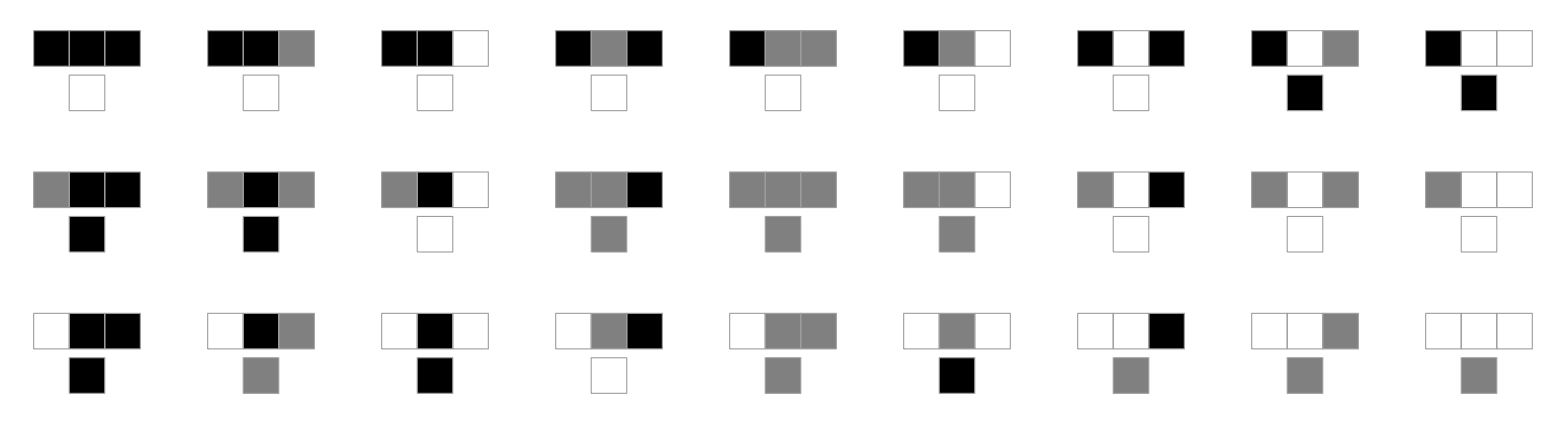
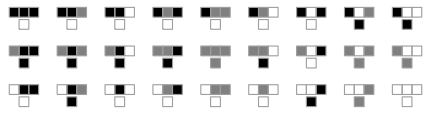
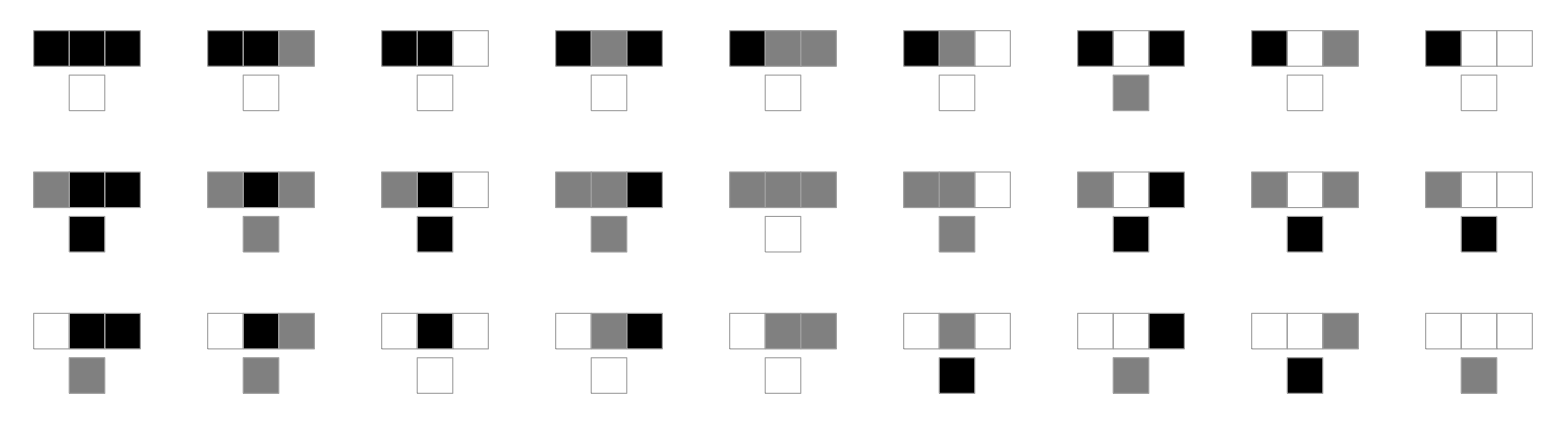

```mathematica
RulePlot[CellularAutomaton[{#, 3, 1}]]&/@ {3450663328, 3484741764, 3822644248}
```

#### Conserving molecules #3

Looking at all possible blockCAs:

```mathematica
Catenate[Table[{1, 0}, 5]]
```

{1,0,1,0,1,0,1,0,1,0}

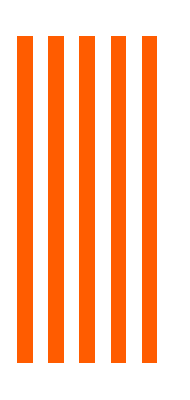
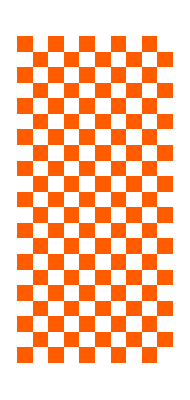
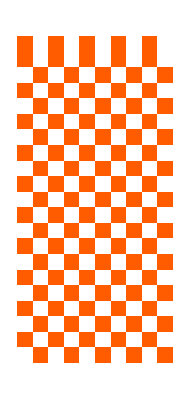
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {Catenate[Table[{1, 0}, 5]], 0}, 20][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@Tuples[Function[tup, tup->#&/@Permutations[tup]]/@Tuples[{0, 1, 2}, 2]]
```

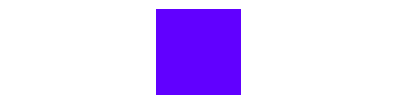
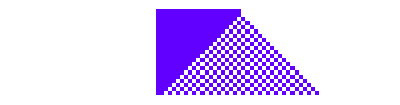
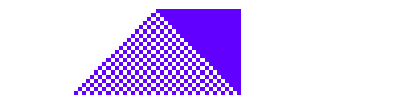
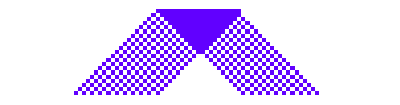
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[Table[2,21],80], 0}, 20][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@Tuples[Function[tup, tup->#&/@Permutations[tup]]/@Tuples[{0, 1, 2}, 2]]
```

```mathematica
ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[Join[Table[1, 10],Table[2,10]],80], 0}, 20][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@Tuples[Function[tup, tup->#&/@Permutations[tup]]/@Tuples[{0, 1, 2}, 2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[RandomChoice[{1, 2}, 20],80], 0}, 20][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&[Tuples[Function[tup, tup->#&/@Permutations[tup]]/@Tuples[{0, 1, 2}, 2]][[5]]]
```

-Graphics-

```mathematica
ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[RandomChoice[{1, 2}, 20],80], 0}, 20][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&[Tuples[Function[tup, tup->#&/@Permutations[tup]]/@Tuples[{0, 1, 2}, 2]][[5]]]
```

```mathematica
{{}}
```

```mathematica
ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[Join[Table[1, 10],Table[2,10]],80], 0}, 20][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@Tuples[Function[tup, tup->#&/@Permutations[tup]]/@Tuples[{0, 1, 2}, 2]]
```

```mathematica
{{"[◼]", "CommaRow"}}[ArrayPlot[Map[First,
ResourceFunction["BlockCellularAutomaton"][
{{{0,0}->{0,0},{0,1}->{1,0},{1,0}->{0,1},{1,1}->{1,1}},2},{#,0},60]],
FrameStyle->GrayLevel[0.7],
ColorRules->{1->{{"[◼]", "SecondLawColors"}}["Reds",1],0->White},
ImageSize->150, Mesh->True]&/@{Normal[SparseArray[{5->1,12->1,17->1},40]]}]
```

-Graphics-

```mathematica
GraphicsRow[ArrayPlot[#,ColorRules->{0->White,
1->{{"[◼]", "SecondLawColors"}}["Reds",3],
2->{{"[◼]", "SecondLawColors"}}["Reds",1]},
FrameStyle->GrayLevel[0.7]
]&/@Partition[Map[First,
ResourceFunction["BlockCellularAutomaton"][{{{2,2}->{1,1},{1,1}->{2,2},{1,2}->{1,2},{2,1}->{2,1},{2,0}->{0,2},{1,0}->{1,0},{0,2}->{2,0},
{0,1}->{0,1},{0,0}->{0,0}},2},
{CenterArray[Table[2,21],80],0},1500]],300],10]
```

```mathematica
Tuples[Function[tup, tup->#&/@Permutations[tup]]/@Tuples[{0, 1, 2}, 2]][[1]]
```

{{0,0}→{0,0},{0,1}→{0,1},{0,2}→{0,2},{1,0}→{1,0},{1,1}→{1,1},{1,2}→{1,2},{2,0}→{2,0},{2,1}→{2,1},{2,2}→{2,2}}

```mathematica
Tuples[Function[tup, tup->#&/@Permutations[tup]]/@Tuples[{0, 1, 2}, 2]]
```

64

```mathematica
ResourceFunction["BlockCellularAutomaton",ResourceSystemBase->"https://www.wolframcloud.com/obj/resourcesystem/api/1.0"][{{0,0}->{0,0},{0,1}->{1,0},{1,0}->{0,1},{1,1}->{1,1}},{Normal[SparseArray[{2->1,7->1},10]],0},3]
```

{{{0,1,0,0,0,0,1,0,0,0},0},{{1,0,0,0,0,0,0,1,0,0},1},{{0,0,0,0,0,0,0,0,1,1},0},{{0,0,0,0,0,0,0,0,1,1},1}}

#### More colors

```mathematica
Module[
{deep=4000},
SeedRandom[426781];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
caf = CellularAutomaton[ru, {Join[Table[1,5], Table[2, 5], Table[3,5]] ,0},{{{10}}, 14}],
loss = Count[Join[Table[2, 5],Table[3,5], Table[1,5]] - caf, Except[0]],
If[loss<=Last[#],{ru,loss},#]
]&,{{0,4,1},Infinity},deep]];
```

```mathematica
ListStepPlot[evo[[All, -1]], PlotRange->All]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[#,{Join[Table[1,5], Table[2, 5], Table[3,5]], 0}, {10, 14}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True]&/@ GatherBy[evo, Last][[2;;, -1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[
{deep=4000},
SeedRandom[426782];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
caf = CellularAutomaton[ru, {Join[Table[1,5], Table[2, 5], Table[3,5]] ,0},{{{10}}, 14}],
loss = Count[Join[Table[2, 5],Table[3,5], Table[1,5]] - caf, Except[0]],
If[loss<=Last[#],{ru,loss},#]
]&,{{0,4,1},Infinity},deep]];
```

```mathematica
ListStepPlot[evo[[All, -1]], PlotRange->All]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[#,{Join[Table[1,5], Table[2, 5], Table[3,5]], 0}, {10, 14}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True]&/@ GatherBy[evo, Last][[2;;, -1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Starting from random initial rule

```mathematica
Module[
{deep=4000},
SeedRandom[426782];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
caf = CellularAutomaton[ru, {Join[Table[1,5], Table[2, 5], Table[3,5]] ,0},{{{10}}, 14}],
loss = Count[Join[Table[2, 5],Table[3,5], Table[1,5]] - caf, Except[0]],
If[loss<=Last[#],{ru,loss},#]
]&,{{ResourceFunction["RandomCA"][{4, 1}]["RuleNumber"], 4, 1},Infinity},deep]];
```

```mathematica
ListStepPlot[evo[[All, -1]], PlotRange->All]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[#,{Join[Table[1,5], Table[2, 5], Table[3,5]], 0}, {10, 14}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True]&/@ GatherBy[evo, Last][[2;;, -1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### With perturbations to the initial conditions

```mathematica
Module[
{deep=4000},
SeedRandom[426782];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
cafs = Table[CellularAutomaton[ru, {MapAt[RandomChoice[Delete[Range[0, 3], # + 1]]&, Join[Table[1,5], Table[2, 5], Table[3,5]],RandomChoice[Range[15]]] ,0},{{{10}}, 14}], 5],
loss = Mean[Count[Join[Table[2, 5],Table[3,5], Table[1,5]] - #, Except[0]]&/@cafs],
If[loss<=Last[#],{ru,loss},#]
]&,{{ResourceFunction["RandomCA"][{4, 1}]["RuleNumber"], 4, 1},Infinity},deep]];
```

```mathematica
ListStepPlot[evo[[All, -1]], PlotRange->All]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[#,{Join[Table[1,5], Table[2, 5], Table[3,5]], 0}, {10, 14}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True]&/@ GatherBy[evo, Last][[2;;, -1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[CellularAutomaton[ru, {MapAt[RandomChoice[Delete[Range[0, 3], # + 1]]&, Join[Table[1,5], Table[2, 5], Table[3,5]],RandomChoice[Range[15]]] ,0},{10, 14}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True, ImageSize->100], 5]&/@ GatherBy[evo, Last][[2;;, -1, 1]]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

#### From random initial conditions

```mathematica
Module[
{deep=6000},
SeedRandom[426782];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
cafs = Table[CellularAutomaton[ru, {RandomChoice[Range[0, 3], 15] ,0},{{{10}}, 14}],5],
loss = Mean[Count[Join[Table[2, 5],Table[3,5], Table[1,5]] - #, Except[0]]&/@cafs],
If[loss<=Last[#],{ru,loss},#]
]&,{{ResourceFunction["RandomCA"][{4, 1}]["RuleNumber"], 4, 1},Infinity},deep]];
```

```mathematica
ListStepPlot[evo[[All, -1]], PlotRange->All]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[#,{RandomChoice[Range[0, 3], 15], 0}, {10, 14}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True]&/@ GatherBy[evo, Last][[2;;, -1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Engineered solution: bubble sort:

```mathematica
ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[RandomChoice[{1, 2}, 20],80], 0}, 20][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&[{{0,0}->{0,0},{0,1}->{0,1},{0,2}->{0,2},{1,0}->{1,0},{1,1}->{1,1},{1,2}->{2, 1},{2,0}->{2,0},{2,1}->{2,1},{2,2}->{2,2}}]
```

-Graphics-

```mathematica
Table[ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[RandomChoice[{1, 2}, 20],40], 0}, 20][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&[{{0,0}->{0,0},{0,1}->{0,1},{0,2}->{0,2},{1,0}->{1,0},{1,1}->{1,1},{1,2}->{2, 1},{2,0}->{2,0},{2,1}->{2,1},{2,2}->{2,2}}], 30]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Enumerating conserving rules for larger rule space

#### k = 4 r = 2 block CAs

```mathematica
SeedRandom[444333];
ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[Join[Table[1, 10],Table[2,10], Table[3,10]],60], 0}, 200][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@RandomSample[Tuples[Function[tup, tup->#&/@Permutations[tup]]/@Tuples[Range[0, 3], 2]],100]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[333344];ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[RandomChoice[Range[0, 3], 30],60], 0}, 20][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@RandomSample[Tuples[Function[tup, tup->#&/@Permutations[tup]]/@Tuples[Range[0, 3], 2]], 100]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[333345];ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[RandomChoice[Range[0, 3], 5],60], 0}, 20][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@RandomSample[Tuples[Function[tup, tup->#&/@Permutations[tup]]/@Tuples[Range[0, 3], 2]], 100]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### k = 4 r = 3 block CAs

```mathematica
Times@@(Length/@Function[tup, tup->#&/@Permutations[tup]]/@Tuples[Range[0, 3], 3])
```

711205618873489693059276793410748416

```mathematica
Table[ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[RandomChoice[Range[0, 3], 30],60], 0}, 100][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&[#->RandomChoice[Permutations[#]]&/@ Tuples[Range[0, 3], 3]], 50]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[RandomChoice[Range[1, 3], 30],60], 0}, 100][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&[#->RandomChoice[Permutations[#]]&/@ Tuples[Range[0, 3], 3]], 50]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
SeedRandom[333222 + i];ListLinePlot[Mean/@ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[RandomChoice[Range[0, 3], 30],60], 0}, 100][[All, 1]]]&[#->RandomChoice[Permutations[#]]&/@ Tuples[Range[0, 3], 3]], {i, 50}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[RandomChoice[Range[0, 3], 30],420], 0}, 100][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&[#->RandomChoice[Permutations[#]]&/@ Tuples[Range[0, 3], 3]], 50]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Engineered solution for k = 4 r = 3 bcas

```mathematica
#->SortBy[#, Which[# == 2, 1,# == 3, 2,# == 1, 1]  Tuples[Range[0, 3], 3]
```

{{0,0,0},{0,0,1},{0,0,2},{0,0,3},{0,1,0},{0,1,1},{0,1,2},{0,1,3},{0,2,0},{0,2,1},{0,2,2},{0,2,3},{0,3,0},{0,3,1},{0,3,2},{0,3,3},{1,0,0},{1,0,1},{1,0,2},{1,0,3},{1,1,0},{1,1,1},{1,1,2},{1,1,3},{1,2,0},{1,2,1},{1,2,2},{1,2,3},{1,3,0},{1,3,1},{1,3,2},{1,3,3},{2,0,0},{2,0,1},{2,0,2},{2,0,3},{2,1,0},{2,1,1},{2,1,2},{2,1,3},{2,2,0},{2,2,1},{2,2,2},{2,2,3},{2,3,0},{2,3,1},{2,3,2},{2,3,3},{3,0,0},{3,0,1},{3,0,2},{3,0,3},{3,1,0},{3,1,1},{3,1,2},{3,1,3},{3,2,0},{3,2,1},{3,2,2},{3,2,3},{3,3,0},{3,3,1},{3,3,2},{3,3,3}}

### Adapting k = 4 r = 3 BCAs

#### Attempt #1

```mathematica
#->RandomChoice[Permutations[#]]&/@ Tuples[Range[0, 3], 3]
```

{{0,0,0}→{0,0,0},{0,0,1}→{0,0,1},{0,0,2}→{2,0,0},{0,0,3}→{0,0,3},{0,1,0}→{0,0,1},{0,1,1}→{0,1,1},{0,1,2}→{1,2,0},{0,1,3}→{0,3,1},{0,2,0}→{2,0,0},{0,2,1}→{2,1,0},{0,2,2}→{2,0,2},{0,2,3}→{2,3,0},{0,3,0}→{0,3,0},{0,3,1}→{3,1,0},{0,3,2}→{3,0,2},{0,3,3}→{0,3,3},{1,0,0}→{1,0,0},{1,0,1}→{1,1,0},{1,0,2}→{0,1,2},{1,0,3}→{3,1,0},{1,1,0}→{0,1,1},{1,1,1}→{1,1,1},{1,1,2}→{1,2,1},{1,1,3}→{3,1,1},{1,2,0}→{2,1,0},{1,2,1}→{1,2,1},{1,2,2}→{2,1,2},{1,2,3}→{3,1,2},{1,3,0}→{3,0,1},{1,3,1}→{1,1,3},{1,3,2}→{3,2,1},{1,3,3}→{3,1,3},{2,0,0}→{0,2,0},{2,0,1}→{2,0,1},{2,0,2}→{2,2,0},{2,0,3}→{2,0,3},{2,1,0}→{0,2,1},{2,1,1}→{2,1,1},{2,1,2}→{2,1,2},{2,1,3}→{1,2,3},{2,2,0}→{2,2,0},{2,2,1}→{1,2,2},{2,2,2}→{2,2,2},{2,2,3}→{3,2,2},{2,3,0}→{3,0,2},{2,3,1}→{3,1,2},{2,3,2}→{2,3,2},{2,3,3}→{3,3,2},{3,0,0}→{0,3,0},{3,0,1}→{0,1,3},{3,0,2}→{3,2,0},{3,0,3}→{0,3,3},{3,1,0}→{1,3,0},{3,1,1}→{3,1,1},{3,1,2}→{2,3,1},{3,1,3}→{3,3,1},{3,2,0}→{2,0,3},{3,2,1}→{3,2,1},{3,2,2}→{2,2,3},{3,2,3}→{2,3,3},{3,3,0}→{0,3,3},{3,3,1}→{3,3,1},{3,3,2}→{3,2,3},{3,3,3}→{3,3,3}}

```mathematica
ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, {CenterArray[RandomChoice[Range[0, 3], 30],60], 0}, 50][[All, 1]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&[#->RandomChoice[Permutations[#]]&/@ Tuples[Range[0, 3], 3]]
```

-Graphics-

```mathematica
CenterArray[Join[Table[2,10], Table[3, 10], Table[1,10]],60]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length/@cafs
```

{60,60,60,60,60}

```mathematica
ru
```

{114628831166361141189113137180082670372,RandomChoice[Permutations[4]],1}

```mathematica
#->RandomChoice[Permutations[#]]&/@ Tuples[Range[0, 3], 3]
```

{{0,0,0}→{0,0,0},{0,0,1}→{0,0,1},{0,0,2}→{0,0,2},{0,0,3}→{0,3,0},{0,1,0}→{0,1,0},{0,1,1}→{1,0,1},{0,1,2}→{2,1,0},{0,1,3}→{1,0,3},{0,2,0}→{0,2,0},{0,2,1}→{2,0,1},{0,2,2}→{0,2,2},{0,2,3}→{2,3,0},{0,3,0}→{0,3,0},{0,3,1}→{1,0,3},{0,3,2}→{3,2,0},{0,3,3}→{0,3,3},{1,0,0}→{0,1,0},{1,0,1}→{1,1,0},{1,0,2}→{2,1,0},{1,0,3}→{0,1,3},{1,1,0}→{0,1,1},{1,1,1}→{1,1,1},{1,1,2}→{2,1,1},{1,1,3}→{3,1,1},{1,2,0}→{2,0,1},{1,2,1}→{2,1,1},{1,2,2}→{2,2,1},{1,2,3}→{1,3,2},{1,3,0}→{3,0,1},{1,3,1}→{3,1,1},{1,3,2}→{2,1,3},{1,3,3}→{1,3,3},{2,0,0}→{0,0,2},{2,0,1}→{2,1,0},{2,0,2}→{2,0,2},{2,0,3}→{2,3,0},{2,1,0}→{2,1,0},{2,1,1}→{1,1,2},{2,1,2}→{2,1,2},{2,1,3}→{3,1,2},{2,2,0}→{2,2,0},{2,2,1}→{2,1,2},{2,2,2}→{2,2,2},{2,2,3}→{2,3,2},{2,3,0}→{2,3,0},{2,3,1}→{1,2,3},{2,3,2}→{2,2,3},{2,3,3}→{2,3,3},{3,0,0}→{3,0,0},{3,0,1}→{1,0,3},{3,0,2}→{2,0,3},{3,0,3}→{3,0,3},{3,1,0}→{0,1,3},{3,1,1}→{1,3,1},{3,1,2}→{3,2,1},{3,1,3}→{3,1,3},{3,2,0}→{3,2,0},{3,2,1}→{2,1,3},{3,2,2}→{2,3,2},{3,2,3}→{3,2,3},{3,3,0}→{3,0,3},{3,3,1}→{3,3,1},{3,3,2}→{2,3,3},{3,3,3}→{3,3,3}}

```mathematica
ruidx
```

26

```mathematica
ru
```

{{0,0,0}→{0,0,0},{0,0,1}→{0,0,1},{0,0,2}→{0,2,0},{0,0,3}→{3,0,0},{0,1,0}→{1,0,0},{0,1,1}→{1,1,0},{0,1,2}→{0,2,1},{0,1,3}→{1,3,0},{0,2,0}→{0,0,2},{0,2,1}→{0,1,2},{0,2,2}→{0,2,2},{0,2,3}→{0,3,2},{0,3,0}→{3,0,0},{0,3,1}→{3,1,0},{0,3,2}→{2,0,3},{0,3,3}→{0,3,3},{1,0,0}→{0,0,1},{1,0,1}→{1,1,0},{1,0,2}→{1,0,2},{1,0,3}→{1,0,3},{1,1,0}→{1,0,1},{1,1,1}→{1,1,1},{1,1,2}→{1,1,2},{1,1,3}→{3,1,1},{1,2,0}→{1,0,2},{114628831166361141189113137180082670372,RandomChoice[Permutations[4]],1}⟦26⟧,{1,2,2}→{2,2,1},{1,2,3}→{3,1,2},{1,3,0}→{3,0,1},{1,3,1}→{1,3,1},{1,3,2}→{1,2,3},{1,3,3}→{3,1,3},{2,0,0}→{0,0,2},{2,0,1}→{1,2,0},{2,0,2}→{0,2,2},{2,0,3}→{2,3,0},{2,1,0}→{1,2,0},{2,1,1}→{2,1,1},{2,1,2}→{2,2,1},{2,1,3}→{2,3,1},{2,2,0}→{2,2,0},{2,2,1}→{1,2,2},{2,2,2}→{2,2,2},{2,2,3}→{3,2,2},{2,3,0}→{2,0,3},{2,3,1}→{3,2,1},{2,3,2}→{2,2,3},{2,3,3}→{2,3,3},{3,0,0}→{0,0,3},{3,0,1}→{0,3,1},{3,0,2}→{2,3,0},{3,0,3}→{3,0,3},{3,1,0}→{3,1,0},{3,1,1}→{3,1,1},{3,1,2}→{2,3,1},{3,1,3}→{3,1,3},{3,2,0}→{3,2,0},{3,2,1}→{1,2,3},{3,2,2}→{2,3,2},{3,2,3}→{2,3,3},{3,3,0}→{3,0,3},{3,3,1}→{3,1,3},{3,3,2}→{3,3,2},{3,3,3}→{3,3,3}}

```mathematica
ru
```

{{0,0,0}→{0,0,0},{0,0,1}→{0,0,1},{0,0,2}→{0,2,0},{0,0,3}→{3,0,0},{0,1,0}→{1,0,0},{0,1,1}→{1,1,0},{0,1,2}→{0,2,1},{0,1,3}→{1,3,0},{0,2,0}→{0,0,2},{0,2,1}→{0,1,2},{0,2,2}→{0,2,2},{0,2,3}→{0,3,2},{0,3,0}→{3,0,0},{0,3,1}→{3,1,0},{0,3,2}→{2,0,3},{0,3,3}→{0,3,3},{1,0,0}→{0,0,1},{1,0,1}→{1,1,0},{1,0,2}→{1,0,2},{1,0,3}→{1,0,3},{1,1,0}→{1,0,1},{1,1,1}→{1,1,1},{1,1,2}→{1,1,2},{1,1,3}→{3,1,1},{1,2,0}→{1,0,2},{1,2,1}→{1,1,2},{1,2,2}→{2,2,1},{1,2,3}→{3,1,2},{1,3,0}→{3,0,1},{1,3,1}→{1,3,1},{1,3,2}→{1,2,3},{1,3,3}→{3,1,3},{2,0,0}→{0,0,2},{2,0,1}→{1,2,0},{2,0,2}→{0,2,2},{2,0,3}→{2,3,0},{2,1,0}→{1,2,0},{2,1,1}→{2,1,1},{2,1,2}→{2,2,1},{2,1,3}→{2,3,1},{2,2,0}→{2,2,0},{2,2,1}→{1,2,2},{2,2,2}→{2,2,2},{2,2,3}→{3,2,2},{2,3,0}→{2,0,3},{2,3,1}→{3,2,1},{2,3,2}→{2,2,3},{2,3,3}→{2,3,3},{3,0,0}→{0,0,3},{3,0,1}→{0,3,1},{3,0,2}→{2,3,0},{3,0,3}→{3,0,3},{3,1,0}→{3,1,0},{3,1,1}→{3,1,1},{3,1,2}→{2,3,1},{3,1,3}→{3,1,3},{3,2,0}→{3,2,0},{3,2,1}→{1,2,3},{3,2,2}→{2,3,2},{3,2,3}→{2,3,3},{3,3,0}→{3,0,3},{3,3,1}→{3,1,3},{3,3,2}→{3,3,2},{3,3,3}→{3,3,3}}

```mathematica
cafs
```

{{ReplaceAll[{0,0,0}]},{ReplaceAll[{0,0,0}]},{ReplaceAll[{0,0,0}]},{ReplaceAll[{0,0,0}]},{ReplaceAll[{0,0,0}]}}

```mathematica
MapAt[RandomChoice[Delete[Range[0, 3], # + 1]]&, CenterArray[Join[Table[1,10], Table[2, 10], Table[3,10]],60],RandomChoice[Range[15, 45]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,3,3,3,3,3,3,3,3,3,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ResourceFunction["BlockCellularAutomaton"][ru, MapAt[RandomChoice[Delete[Range[0, 3], # + 1]]&, CenterArray[Join[Table[1,10], Table[2, 10], Table[3,10]],60],RandomChoice[Range[15, 45]]] ,{{{50}}}]
```

Catenate::invrp: The argument 0 is not a valid Association or a list.

ReplaceAll::reps: {0,0,0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of ReplaceAll::argt will be suppressed during this calculation.

{ReplaceAll[{0,0,0}]}

```mathematica
Module[
{deep=1},
SeedRandom[426782];
evo=NestList[CompoundExpression[
ruidx = RandomInteger[{1, Length[First[#]]}],
ru=ReplacePart[First[#], ruidx-> RandomChoice[Permutations[First[#][[ruidx]]]]],
cafs = Table[ResourceFunction["BlockCellularAutomaton"][ru, MapAt[RandomChoice[Delete[Range[0, 3], # + 1]]&, CenterArray[Join[Table[1,10], Table[2, 10], Table[3,10]],60],RandomChoice[Range[15, 45]]] ,{{{50}}}], 5],
loss = Mean[Count[CenterArray[Join[Table[2,10], Table[3, 10], Table[1,10]],60] - #, Except[0]]&/@cafs],
If[loss<=Last[#],{ru,loss},#]
]&,{#->RandomChoice[Permutations[#]]&/@ Tuples[Range[0, 3], 3],Infinity},deep]];
```

Catenate::invrp: The argument 0 is not a valid Association or a list.

ReplaceAll::reps: {0,0,0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of ReplaceAll::argt will be suppressed during this calculation.

Catenate::invrp: The argument 0 is not a valid Association or a list.

General::stop: Further output of Catenate::invrp will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,«10»}+{-ReplaceAll[{0,0,0}]} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

```mathematica
ListStepPlot[evo[[All, -1]], PlotRange->All]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[ru, MapAt[RandomChoice[Delete[Range[0, 3], # + 1]]&, CenterArray[Join[Table[1,10], Table[2, 10], Table[3,10]],60],RandomChoice[Range[15, 45]]] ,50], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@ GatherBy[evo, Last][[2;;, -1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Attempt #2

```mathematica
RandomChoice[Rest[Permutations[{Table[1,10], Table[2, 10], Table[3,10]}]]]
```

{{2,2,2,2,2,2,2,2,2,2},{3,3,3,3,3,3,3,3,3,3},{1,1,1,1,1,1,1,1,1,1}}

```mathematica
ResourceFunction["BlockCellularAutomaton"][ru, MapAt[RandomChoice[Delete[Range[0, 3], # + 1]]&, CenterArray[Join[Table[2,10], Table[3, 10], Table[1,10]],60],RandomChoice[Range[15, 45]]] ,{{{50}}, 60}]
```

Catenate::invrp: The argument 0 is not a valid Association or a list.

ReplaceAll::reps: {0,0,0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of ReplaceAll::argt will be suppressed during this calculation.

{ReplaceAll[{0,0,0}]}

```mathematica
Module[
{deep=1000},
SeedRandom[426782];
evo=NestList[CompoundExpression[
ruidx = RandomInteger[{1, Length[First[#]]}],
ru=ReplacePart[First[#], ruidx-> RandomChoice[Permutations[First[#][[ruidx]]]]],
cafs = Table[ResourceFunction["BlockCellularAutomaton"][ru, MapAt[RandomChoice[Delete[Range[0, 3], # + 1]]&, CenterArray[Join[Table[2,10], Table[3, 10], Table[1,10]],60],RandomChoice[Range[15, 45]]] ,{{{50}}}], 5],
loss = Mean[Count[CenterArray[Join[Table[1,10], Table[2, 10], Table[3,10]],60] - #, Except[0]]&/@cafs],
If[loss<=Last[#],{ru,loss},#]
]&,{#->RandomChoice[Permutations[#]]&/@ Tuples[Range[0, 3], 3],Infinity},deep]];
```

Catenate::invrp: The argument 0 is not a valid Association or a list.

ReplaceAll::reps: {0,0,0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of ReplaceAll::argt will be suppressed during this calculation.

Catenate::invrp: The argument 0 is not a valid Association or a list.

General::stop: Further output of Catenate::invrp will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,0,0,0,0,0,«10»}+{-ReplaceAll[{0,0,0}]} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

$Aborted

```mathematica
ListStepPlot[evo[[All, -1]], PlotRange->All]
```

-Graphics-

```mathematica
ArrayPlot[ResourceFunction["BlockCellularAutomaton"][#, MapAt[RandomChoice[Delete[Range[0, 3], # + 1]]&, CenterArray[Join[Table[2,10], Table[3, 10], Table[1,10]],60],RandomChoice[Range[15, 45]]] ,50], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@ GatherBy[evo, Last][[2;;, -1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Outtakes

```mathematica
caf
```

{2,2,2,2,2,0,2,1,0,1}

```mathematica
Count[Join[Table[2, 5], Table[1,5]] - caf, Except[0]]
```

3

```mathematica
loss
```

3

```mathematica
ArrayPlot[CellularAutomaton[evo[[-1, 1]], {Join[Table[1,5], Table[2, 5]],0},{10, 9}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], Mesh->True]
```

-Graphics-

```mathematica
Module[
{deep=5000},
SeedRandom[426780];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
caf = CellularAutomaton[ru, {Join[Table[1,5], Table[2, 5]] ,0},{{{30}}, 9}],
loss = Count[Join[Table[1,5], Table[2, 5]] - caf, Except[0]],
If[loss<=Last[#],{ru,loss},#]
]&,{{0,3,1},Infinity},deep]];
```

```mathematica
ListStepPlot[evo[[All, -1]]]
```

-Graphics-

```mathematica
evo[[-1, -1]]
```

1

```mathematica
caf
```

{1,1,1,1,1,2,1,2,2,2}

```mathematica
ArrayPlot[CellularAutomaton[evo[[-1, 1]], {Join[Table[1,5], Table[2, 5]],0},{30, 9}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]
```

-Graphics-